## Chiral bands in ^132 La

```mathematica
band1=Sort[{5219,4200.2,3206.2,2300.5,1522.9,936.0,775.0}];
band2=Sort[{4759.2,3713.2,2754.1,1915.2,1229.0}];
band3=Sort[{3617.0,2701.0,1918.0}];
band4=Sort[{3127.8,2298.0,1558.0}];
spin1=Table[If[i==8,9,i],{i,8,20,2}];
spin2=Table[i,{i,11,19,2}];
spin3=Table[i,{i,12,16,2}];
spin4=Table[i,{i,11,15,2}];
```

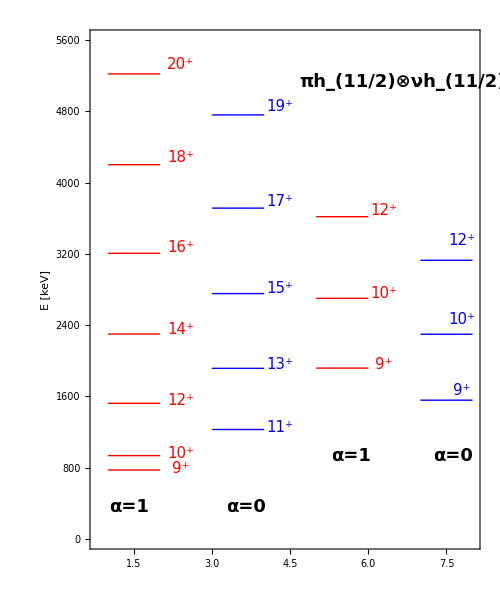

```mathematica
bandmaker[shift_,data_]:=Table[{{1+shift,data[[i]]},{2+shift,data[[i]]}},{i,1,Length[data]}];
p1[band_]:=ListLinePlot[bandmaker[0,band],PlotRange->{{0.8,8},{0,5600}},AspectRatio->1.2,Frame->{False,True,False,False},FrameStyle->Directive[Black,Thick],Axes->False,PlotStyle->Directive[Red,Thick],FrameLabel->{"","E [keV]"},LabelStyle->{18,Bold,Black}];
p2[band_]:=ListLinePlot[bandmaker[2,band],PlotStyle->Directive[Blue,Thick]];
p3[band_]:=ListLinePlot[bandmaker[4,band],PlotStyle->Directive[Red,Thick]];
p4[band_]:=ListLinePlot[bandmaker[6,band],PlotStyle->Directive[Blue,Thick]];
shower[band1_,band2_,band3_,band4_]:=Show[p1[band1],p2[band2],p3[band3],p4[band4],Epilog->{Table[Inset[Style[StringTemplate["(``)^+"][spin1[[i]]],Red,Italic,15],{2.4,band1[[i]]+0.02band1[[i]]}],{i,1,Length[band1]}],Table[Inset[Style[StringTemplate["(``)^+"][spin2[[i]]],Blue,Italic,15],{4.3,band2[[i]]+0.02band2[[i]]}],{i,1,Length[band2]}],Table[Inset[Style[StringTemplate["(``)^+"][spin1[[i]]],Red,Italic,15],{6.3,band3[[i]]+0.02band3[[i]]}],{i,1,Length[band3]}],Table[Inset[Style[StringTemplate["(``)^+"][spin1[[i]]],Blue,Italic,15],{7.8,band4[[i]]+0.07band4[[i]]}],{i,1,Length[band4]}],Inset[Style["α=1",Bold,Black,18],Scaled[{0.1,0.08}]],Inset[Style["α=0",Bold,Black,18],Scaled[{0.4,0.08}]],Inset[Style["α=1",Bold,Black,18],Scaled[{0.67,0.18}]],Inset[Style["α=0",Bold,Black,18],Scaled[{0.93,0.18}]],Inset[Style["πh_(11/2)⊗νh_(11/2)",Bold,Black,18],Scaled[{0.8,0.9}]]},ImageSize->500];
shower[band1,band2,band3,band4]
```